```mathematica
resultsDirectory=FileNameJoin[{ParentDirectory@NotebookDirectory[],"results"}]
```

/Users/christopher/git/bitcoin-rs-experiments/results

```mathematica
uniqueMinersRaw=Import@FileNameJoin[{resultsDirectory,"number_unique_miners_over_time.json"}];
```

```mathematica
uniqueMiners=TimeSeries@GroupBy[uniqueMinersRaw,FromUnixTime@*First->Last,First]
```

TimeSeries[…]

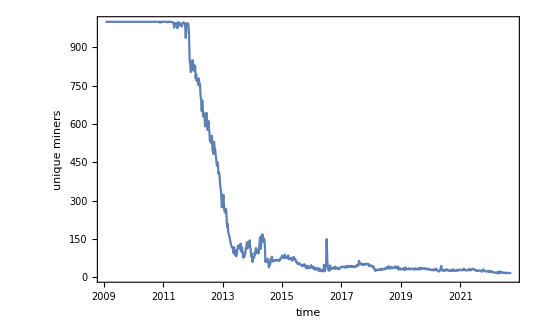

```mathematica
DateListPlot[uniqueMiners,FrameLabel->{"time","unique miners"}]
```

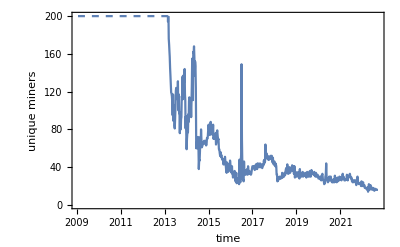

```mathematica
DateListPlot[uniqueMiners,FrameLabel->{"time","unique miners"},PlotRange->{All,{0,200}},ClippingStyle->Dashed]
```

```mathematica
uniqueMiners["LastValue"]
```

16

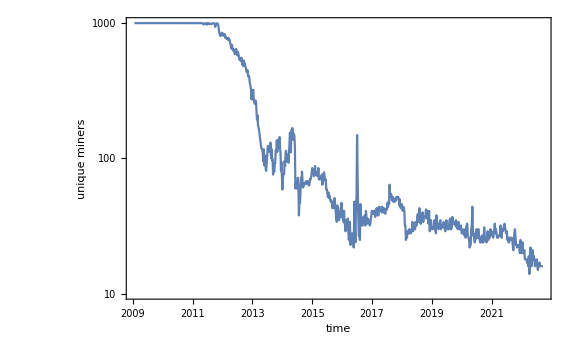

```mathematica
DateListLogPlot[uniqueMiners,FrameLabel->{"time","unique miners"}]
```